Your Title Here

```mathematica
Manipulate[
Module[{a,b,r,GibbsEnergy,molarComposition1,molarComposition2,beaker,plot},
a=7500;b=1000;r=8.314 ;(*J/mol*) 

GibbsEnergy [x_]:=x*(1-x)*(a+b*(1-2*x))+r*t*(x*Log[x]+(1-x)Log[1-x]);
molarComposition1=x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.0001}]];
molarComposition2= x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.9999}]];


beaker=Graphics3D[{
{Opacity@0.3,Cylinder[{{0,0,0},{0,0,1.75}},1]},
{EdgeForm@None,
If[molarComposition1==molarComposition2,
{Opacity[0.8,Blend[{Blue,RGBColor[0,0.6,0]},0.5]],Cylinder [{{0,0,0}, {0,0,1.5}}, 1],
Text[Framed[Style[Column[{"mole fraction",NumberForm[molarComposition1,{2,2}]},Center],18,Black],Background->White,FrameStyle->None,FrameMargins->Small],{0,0,0.75}]
},
{Opacity[0.8,Blue],Cylinder [{{0,0,0}, {0,0, 0.75}}, 1],Opacity [0.8,RGBColor[0,0.6,0]],Cylinder [{{0,0,0.75}, {0,0, 1.5}}, 1],
Text[Framed[Style[NumberForm[#1,{2,2}],18,Black],Background->White,FrameStyle->None,FrameMargins->Small],{0,0,#2}]&@@@{{molarComposition1,0.375},{molarComposition2,1.125}}
}]
}
 },Boxed->False,ViewPoint->{0,3.5,0},ImageSize->{200,425},AspectRatio->2];

plot=Plot[GibbsEnergy[x], {x, 0.0001, 0.9999},PlotStyle->{Thick,Black},PlotRangePadding->{None,Scaled@0.02},
Axes->False,Frame->True,FrameLabel->{"mole fraction", "change in Gibbs free energy (J/mol)"},LabelStyle->{17,Black},ImageSize->{400,425},AspectRatio->Full,
Epilog->{
Line[{{0,0},{1,0}}],
If[molarComposition1≠molarComposition2,{
{Dashed,
Blue,Line[{{molarComposition1,GibbsEnergy[molarComposition1]}, {molarComposition1, 0}}],
RGBColor[0,0.6,0],Line[{{molarComposition2,GibbsEnergy[molarComposition2]}, {molarComposition2, 0}}]},
{PointSize@0.03,Blue,Point[{molarComposition1,GibbsEnergy[molarComposition1]}],RGBColor[0,0.6,0], Point[{molarComposition2,GibbsEnergy[molarComposition2]}]}
}]
}];

Grid@{{plot,beaker}}
],
Control[{{t,273,"temperature (K)"},273,523,10,Appearance->"Labeled" }]
]
```

```mathematica
Manipulate[
Module[{a,b,r,GibbsEnergy,molarComposition1,molarComposition2,dGibbs,ddGibs,zeroes,list,pos,opt},
a=7500;b=1000;r=8.314 ;(*J/mol*) 

GibbsEnergy [x_]:=x*(1-x)*(a+b*(1-2*x))+r*t*(x*Log[x]+(1-x)Log[1-x]);
molarComposition1=x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.0001}]];
molarComposition2= x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.9999}]];

dGibbs[x_]:=GibbsEnergy'[x];
zeroes[i_]:=x/.FindRoot[dGibbs[x]==0,{x,If[i==1,0.0001,0.9999]}];

list[1]=dGibbs[zeroes[1]-#]&/@Range[0.0001,0.01,0.00001];
list[2]=dGibbs[zeroes[2]-#]&/@Range[0.0001,0.01,0.00001];

pos=Position[If[Abs[list[1][[1]]-#]≤0.1,1,0]&/@list[2],1][[1,1]];



opt=Sequence[PlotStyle->{Thick,Black},PlotRangePadding->{Scaled@0.01,Scaled@0.02},Axes->False,Frame->True,LabelStyle->{17,Black},ImageSize->{350,400},AspectRatio->Full];

Column[{
Grid@{{
Plot[GibbsEnergy[x], {x, 0.0001, 0.9999},Evaluate@opt,Epilog->{Line[{{0,0},{1,0}}]}],
Plot[dGibbs[x],{x,0.0001,0.9999},Evaluate@opt,
Epilog->{PointSize@0.03,
Point@{zeroes[#],dGibbs[zeroes[#]]}&/@Range@2,
Blue,Point@{zeroes[1]-#,dGibbs[zeroes[1]-#]}&/@Range[0.0001,0.01,0.0001]
}]
}},
(*list[1],list[2],*)
pos,list[2][[pos]]
}]
],
Control[{{t,273,"temperature (K)"},273,523,10,Appearance->"Labeled" }]
]
```

```mathematica
Abs[-5.685-(-2.443)]
```

3.242

```mathematica
Manipulate[
Module[{a,b,r,GibbsEnergy,molarComposition1,molarComposition2,dGibbs,ddGibs,zeroes,opt},
a=7500;b=1000;r=8.314 ;(*J/mol*) 

GibbsEnergy [x_]:=x*(1-x)*(a+b*(1-2*x))+r*t*(x*Log[x]+(1-x)Log[1-x]);
molarComposition1=x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.0001}]];
molarComposition2= x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.9999}]];

dGibbs[x_]:=GibbsEnergy'[x];
zeroes[i_]:=x/.FindRoot[dGibbs[x]==0,{x,Switch[i,1,0.0001,2,0.5,3,0.9999]}];

opt=Sequence[PlotStyle->{Thick,Black},PlotRangePadding->{Scaled@0.01,Scaled@0.02},Axes->False,Frame->True,LabelStyle->{17,Black},ImageSize->{350,400},AspectRatio->Full];

Column[{
Grid@{{
Plot[GibbsEnergy[x], {x, 0.0001, 0.9999},Evaluate@opt,Epilog->{Line[{{0,0},{1,0}}]}],
Plot[dGibbs[x],{x,0.0001,0.9999},Evaluate@opt,
Epilog->{PointSize@0.03,
Point@{zeroes[#],dGibbs[zeroes[#]]}&/@Range@3,
Blue,Point@{zeroes[1]-#,dGibbs[zeroes[1]-#]}&/@Range[0.0001,0.01,0.0001]
}]
}},
Simplify@GibbsEnergy[x],
dGibbs[zeroes[1]-#]&/@Range[0.0001,0.01,0.0001],
(*dGibbs[zeroes[2]-#]&/@Range[0.001,0.01,0.001],*)
dGibbs[zeroes[3]-#]&/@Range[0.0001,0.01,0.0001]
}]
],
Control[{{t,273,"temperature (K)"},273,523,10,Appearance->"Labeled" }]
]
```

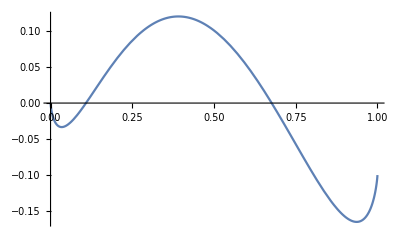

```mathematica
Module[{f},
f[x_]:=1.135*(1-x)*Log[1-x]+x*(4.15-5.25*x+x^2+1.135*Log[x]);

Plot[f[x],{x,0,1}]
]
```

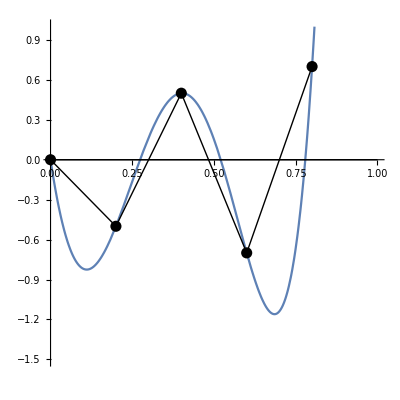

```mathematica
Module[{pts,y},
(*pts={{0,-0.2},{0.2,0.5},{0.4,0.75},{0.8,-0.2},{1,-0.5}};*)
pts={{0,0},{0.2,-0.5},{0.4,0.5},{0.6,-0.7},{0.8,0.7}};
y[x_]:=Fit[pts,{1,z,z^2,z^3,z^4,z^5},z]/.z->x;

Plot[y[x],{x,0,1},Epilog->{PointSize@0.02,Point@pts,Line[pts],Line[{{0,0},{1,0}}]},PlotRange->{{0,1},{-1.5,1}},ImageSize->{400,400},AspectRatio->Full]
]
```





```mathematica
(*If[molarComposition1≠molarComposition2,{
{Dashed,
Blue,Line[{{molarComposition1,GibbsEnergy[molarComposition1]}, {molarComposition1, 0}}],
RGBColor[0,0.6,0],Line[{{molarComposition2,GibbsEnergy[molarComposition2]}, {molarComposition2, 0}}]},
{PointSize@0.03,Blue,Point[{molarComposition1,GibbsEnergy[molarComposition1]}],RGBColor[0,0.6,0], Point[{molarComposition2,GibbsEnergy[molarComposition2]}]}
}]*)
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX